## Pràctica 3: POLINOMIS

### Exercici 1

Executeu les instruccions :

```mathematica
p[x_]:=x^4+2x^3-8x^2+66x+39
```

```mathematica
p[2+3I]
```

0

Amb això heu definit p com una funció en la variable x (observeu la barra baixa) i heu comprovat que z=2+3i és arrel del polinomi p[x]=x^4+2 x^3-8 x^2+66x+39. Comproveu que el conjugat de z també és arrel de p[x].

```mathematica
Conjugate[p[x]]
```

39+66 Conjugate[x]-8 Conjugate[x]^2+2 Conjugate[x]^3+Conjugate[x]^4

Per a calcular les altres arrels i factoritzar p[x] executeu, respectivament, les instruccions següents :

```mathematica
Solve[p==0]
```

{{x→2-3 ⅈ},{x→2+3 ⅈ},{x→-3-√6},{x→-3+√6}}

```mathematica
Factor[p[x]]
```

(13-4 x+x^2) (3+6 x+x^2)

Una altra opció seria definir el polinomi de la forma següent:

```mathematica
p=x^4+2x^3-8x^2+66x+39
```

39+66 x-8 x^2+2 x^3+x^4

En aquest cas, per a avaluar el polinomi p en z_1 hauríem de fer-ho amb la instrucció:

```mathematica
p/.{x->z1}
```

39+66 z1-8 z1^2+2 z1^3+z1^4

I per a calcular les seves arrels i factoritzar-lo, les instruccions

```mathematica
Solve[p==0]
```

{{x→2-3 ⅈ},{x→2+3 ⅈ},{x→-3-√6},{x→-3+√6}}

```mathematica
Factor[p]
```

(13-4 x+x^2) (3+6 x+x^2)

### Exercici 2

a) Useu Solve per a resoldre l'equació x^2+(2+ⅈ)x+2-2 ⅈ=0.

```mathematica
Solve[x^2+(2+I)*x+2-2I==0]
```

{{x→-2-2 ⅈ},{x→ⅈ}}

b) Useu Factor per a trobar les arrels racionals de   p=7614 x^5+486429 x^4-632680 x^3+245280 x^2-28719 x+506  i  q=3 x^3+5 x^2+5x+2. Quina és la descomposició en factors irreductibles de q a ℝ[x]? I a ℂ[x]?

```mathematica
p=7614 x^5+486429 x^4-632680 x^3+245280 x^2-28719 x+506
```

506-28719 x+245280 x^2-632680 x^3+486429 x^4+7614 x^5

```mathematica
Factor[p]
```

```mathematica
(-2+3 x) (-1+47 x) (-23+54 x) (-11+65 x+x^2)
q=3x^3+5x^2+5x+2
```

(-2+3 x) (-1+47 x) (-23+54 x) (-11+65 x+x^2)

2+5 x+5 x^2+3 x^3

```mathematica
Factor[q]
```

(2+3 x) (1+x+x^2)

```mathematica
Solve[q[x]==0]
```

{{(2+5 x+5 x^2+3 x^3)[x]→0}}

```mathematica
Factor[q[x]]
```

(2+5 x+5 x^2+3 x^3)[x]

```mathematica
Decompose[q,x]
```

{2+5 x+5 x^2+3 x^3}

### Exercici 3

Esbrineu que fan les funcions PolynomialQuotient i PolynomialRemainder. Calculeu el quocient i la resta de la divisió entre p i q de l'exercici anterior.

```mathematica
p=7614 x^5+486429 x^4-632680 x^3+245280 x^2-28719 x+506
```

506-28719 x+245280 x^2-632680 x^3+486429 x^4+7614 x^5

```mathematica
q=3x^3+5x^2+5x+2
```

2+5 x+5 x^2+3 x^3

```mathematica
PolynomialQuotient[p,q,x]
```

```mathematica
-1434935/3+157913 x+2538 x^2

PolynomialRemainder[p,q,x]
```

2871388/3+(6141040 x)/3+(5526592 x^2)/3

```mathematica
La funcio PolynominqlQuotient serveix per calcular el quocient entre P i Q
La funció PolynominalRemainder serveix per calcular el residu de dividir P entre Q
```

### Exercici 4

Esbrineu per a què serveix la funció PolynomialGCD i utilitzeu-la per a calcular les arrels comunes dels polinomis p=72 x^5-841 x^4+2892 x^3-2444 x^2+48x+368, i q=72 x^8-409 x^7+150 x^6+92 x^5+72 x^4-337 x^3-259 x^2+242x+92.

```mathematica
p=72 x^5-841 x^4+2892 x^3-2444 x^2+48x+368
```

368+48 x-2444 x^2+2892 x^3-841 x^4+72 x^5

```mathematica
q=72 x^8-409 x^7+150 x^6+92 x^5+72 x^4-337 x^3-259 x^2+242x+92
```

92+242 x-259 x^2-337 x^3+72 x^4+92 x^5+150 x^6-409 x^7+72 x^8

```mathematica
PolynomialGCD[p[x],q[x]]
```

1

```mathematica
La funció PolynominalGCD serveix per calcular el màxim comú divisor de dos polinomis
```

### Exercici 5

Mathematica sap resoldre l'equació quadràtica general, però quan hi ha més d'una variable se li ha d'indicar quin és la que vull resoldre en funció de les altres. 
a) Executeu les següents instruccions:

```mathematica
Solve[a*x^2+b*x+c==0]
Clear[a,b,c]
```

{{c→-4/3 (717847 x+1535260 x^2+1381648 x^3)}}

i

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Quina és la diferència entre una i l'altra?

La diferència es que en la primera no s’ha especificat la variable amb que es vol resoldre en funció de les altres i en cambi en la segona si que s’especifica, que en aquet cas es X.

b) Executeu:

```mathematica
Solve[a*x^3+b*x^2+c*x+d==0,x]
```

{{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)}}

```mathematica
Solve[a*x^4+b*x^3+c*x^2+d*x+e==0,x]
```

{{x→-b/(4 a)-1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))-1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a)-(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))+1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a)-(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))))},{x→-b/(4 a)+1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))-1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a)+(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))))},{x→-b/(4 a)+1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))+1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a)+(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))))}}

```mathematica
Solve[a*x^5+b*x^4+c*x^3+d*x^2+e*x+f==0,x]
```

{{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,1]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,2]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,3]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,4]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,5]}}

c) Calculeu totes les arrels complexes d'aquests polinomis i dibuixeu-les en el plà (useu la funció v[z] definida en la pràctica anterior)

```mathematica
z1=3*x^3-2*x+1
```

1-2 x+3 x^3

```mathematica
w=Solve[z1==0,x]
```

{{x→-1},{x→1/6 (3-ⅈ √3)},{x→1/6 (3+ⅈ √3)}}

```mathematica
s1=x/.w[[1]]
```

-1

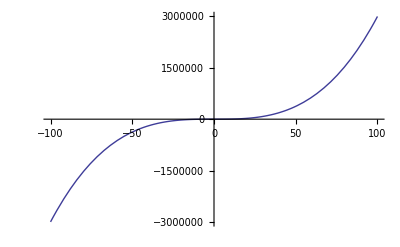

```mathematica
Plot[z1, {x,-100,100}]
```

```mathematica
z2=5*x^4+2*x-6
```

-6+2 x+5 x^4

```mathematica
w2=Solve[z2==0,x]
```

{{x→1/2 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))-1/2 √(-(2 (1+√641))^(1/3)/5^(2/3)+(4 2^(2/3))/(5 (1+√641))^(1/3)-4/(5 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))))},{x→1/2 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))+1/2 √(-(2 (1+√641))^(1/3)/5^(2/3)+(4 2^(2/3))/(5 (1+√641))^(1/3)-4/(5 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))))},{x→-1/2 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))-1/2 √(-(2 (1+√641))^(1/3)/5^(2/3)+(4 2^(2/3))/(5 (1+√641))^(1/3)+4/(5 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))))},{x→-1/2 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))+1/2 √(-(2 (1+√641))^(1/3)/5^(2/3)+(4 2^(2/3))/(5 (1+√641))^(1/3)+4/(5 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))))}}

```mathematica
s2=x/.w2[[2]]
```

1/2 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))+1/2 √(-(2 (1+√641))^(1/3)/5^(2/3)+(4 2^(2/3))/(5 (1+√641))^(1/3)-4/(5 √((2 (1+√641))^(1/3)/5^(2/3)-(4 2^(2/3))/(5 (1+√641))^(1/3))))

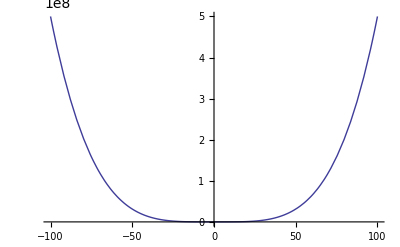

```mathematica
Plot[z2, {x,-100,100}]
```

```mathematica
z3=x^5+x^4+x^3+x^2+x+1
```

1+x+x^2+x^3+x^4+x^5

```mathematica
w3=Solve[z3==0,x]
```

{{x→-1},{x→-(-1)^(1/3)},{x→(-1)^(1/3)},{x→-(-1)^(2/3)},{x→(-1)^(2/3)}}

```mathematica
s3=x/.w3[[3]]
```

(-1)^(1/3)

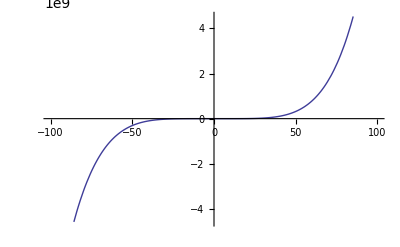

```mathematica
Plot[z3, {x,-100,100}]
```

### Exercici 6

La següent funció calcula arrels de polinomis utilitzant cerca binària. El "input" és un polinomi p[x], un valor a tal que p(a)<0, un valor b tal que p(b)>0, i el nombre d'iteracions n.

```mathematica
BinarySearch[p_,a_,b_,n_]:=Module[{j,A,B,PM},
j:=1;
If[p[a]<0,A:={a},A:={b}];
If[p[b]>0,B:={b},B:={a}];
PM:={(a+b)/2};
While[j<n,AppendTo[A,If[p[PM[[j]]]<0,PM[[j]],A[[j]]]];AppendTo[B,If[p[PM[[j]]]>0,PM[[j]],B[[j]]]];AppendTo[PM,(A[[j+1]]+B[[j+1]])/2];j++];
Return[PM];];
```

Calculem una aproximació de

```mathematica
q[x_]:=x^5-x+1
```

```mathematica
Clear[q]
```

```mathematica
a:=-2
```

```mathematica
b:=0
```

```mathematica
n:=25
```

```mathematica
BinarySearch[q,a,b,n]
```

{-1,-3/2,-5/4,-9/8,-19/16,-37/32,-75/64,-149/128,-299/256,-597/512,-1195/1024,-2391/2048,-4781/4096,-9563/8192,-19125/16384,-38251/32768,-76501/65536,-153001/131072,-306001/262144,-612003/524288,-1224007/1048576,-2448013/2097152,-4896027/4194304,-9792055/8388608,-19584111/16777216}

```mathematica
q[%]
```

{1,-163/32,-821/1024,10583/32768,-182339/1048576,3007787/33554432,-41013851/1073741824,916845563/34359738368,-6062252219/1099511627776,374556657467/35184372088832,2906098288069/1125899906842624,-52689677110327/36028797018963968,645980328865411/1152921504606846976,-16632683962427563/36893488147419103232,64688937656126299/1180591620717411303424,-7480351520965427707/37778931862957161709568,-86560411108690000709/1208925819614629174706176,-325067206708791373513/38685626227668133590597632,28714844967483573783919/1237940039285380274899124224,293005401887825125604333/39614081257132168796771975168,-637796346522777088564199/1267650600228229401496703205376,139814170925933117876013347/40564819207303340847894502572032,1910476179025835844731540629/1298074214633706907132624082305024,20117972912031612850943437673/41538374868278621028243970633760768,-12501329220837089238626245679/1329227995784915872903807060280344576}

```mathematica
N[%]
```

{1.,-5.09375,-0.801758,0.322968,-0.173892,0.089639,-0.0381971,0.0266837,-0.00551359,0.0106455,0.00258113,-0.00146243,0.000560299,-0.00045083,0.0000547937,-0.000198003,-0.0000716011,-8.40279×10^-6,0.0000231957,7.3965×10^-6,-5.03133×10^-7,3.44669×10^-6,1.47178×10^-6,4.84323×10^-7,-9.40495×10^-9}

a) Calculeu una aproximació de les arrels dels següents polinomis

```mathematica
r[x_]:=x^14-8
```

```mathematica
a:= -3
```

```mathematica
b:= 7
```

```mathematica
n:= 14
```

```mathematica
BinarySearch[r,a,b,n]
```

{2,9/2,23/4,51/8,107/16,219/32,443/64,891/128,1787/256,3579/512,7163/1024,14331/2048,28667/4096,57339/8192}

```mathematica
r[%]
```

{16376,22876792323889/16384,11592836322391266161/268435456,805345924685806929889369/4398046511104,25785341501436005641239129161/72057594037927936,583737518747227968516296966261929/1180591620717411303424,11211201728748332035751123541609295721/19342813113834066795298816,198741176545787944071675613725278259608809/316912650057057350374175801344,3386442727369291586536482435470208756949202921/5192296858534827628530496329220096,56580108697341009514052850724228656243404630011369/85070591730234615865843651857942052864,936115241251555442087207748682418728409041310735931881/1393796574908163946345982392040522594123776,15412423857044968684733601257780527525955656378280666460649/22835963083295358096932575511191922182123945984,253134564301591855028898559581128292827457509089776478570914281/374144419156711147060143317175368453031918731001856,4152423147128862318010155714396224220286028519717877605222606111209/6129982163463555433433388108601236734474956488734408704}

```mathematica
s[x_]:=x^24-14*x+1
```

```mathematica
a:=-5
```

```mathematica
b:= 7
```

```mathematica
n:= 12
```

```mathematica
BinarySearch[s, a, b, n]
```

{1,4,5/2,7/4,11/8,19/16,35/32,73/64,143/128,289/256,575/512,1147/1024}

```mathematica
s[%]
```

{-12,281474976710601,59604644204965281/16777216,191574616718613713985/281474976710656,9763549487495240069561889/4722366482869645213696,3660822891675466542817171053921/79228162514264337593543950336,-7605444447601028043760655389862041119/1329227995784915872903807060280344576,190689525033243010098825562186449069805489089/22300745198530623141535718272648361505980416,-131265652306242990852047111335636700866055023704447/374144419156711147060143317175368453031918731001856,22294870859147926552162889496522170940010825150464049376001/6277101735386680763835789423207666416102355444464034512896,155716789368857306778887712700396673785353939206291024302986037761/105312291668557186697918027683670432318895095400549111254310977536,945528533568434884062833839268219637541062629009793039819263338384847265/1766847064778384329583297500742918515827483896875618958121606201292619776}

```mathematica
N[%]
```

{-12.,2.81475×10^14,3.55271×10^9,680610.,2067.51,46.2061,-5.7217,8.55081,-0.350842,3.55178,1.47862,0.53515}

```mathematica
t[x_]:=x^7+x^3+x+12
```

```mathematica
a:= -6
```

```mathematica
b:= 2
```

```mathematica
n:=12
```

```mathematica
BinarySearch[t, a,b,n]
```

{-2,0,-1,-3/2,-5/4,-11/8,-21/16,-43/32,-87/64,-173/128,-345/256,-691/512}

```mathematica
t[%]
```

{-126,12,9,-1275/128,66003/16384,-2656707/2097152,460886499/268435456,10958218845/34359738368,-1975362898215/4398046511104,-33259755750597/562949953421312,9468987201235287/72057594037927936,337002064190217765/9223372036854775808}

```mathematica
N[%]
```

{-126.,12.,9.,-9.96094,4.0285,-1.26682,1.71694,0.318926,-0.449146,-0.0590812,0.131409,0.0365378}

b) Expliqueu per què falla la funció quan executem el següent:

```mathematica
u[x_]:=x^2-64
```

```mathematica
BinarySearch[u,10,15,25]
```

{25/2,55/4,115/8,235/16,475/32,955/64,1915/128,3835/256,7675/512,15355/1024,30715/2048,61435/4096,122875/8192,245755/16384,491515/32768,983035/65536,1966075/131072,3932155/262144,7864315/524288,15728635/1048576,31457275/2097152,62914555/4194304,125829115/8388608,251658235/16777216,503316475/33554432}

```mathematica
q[%]
```

q[{25/2,55/4,115/8,235/16,475/32,955/64,1915/128,3835/256,7675/512,15355/1024,30715/2048,61435/4096,122875/8192,245755/16384,491515/32768,983035/65536,1966075/131072,3932155/262144,7864315/524288,15728635/1048576,31457275/2097152,62914555/4194304,125829115/8388608,251658235/16777216,503316475/33554432}]

```mathematica
N[%]
```

{12.5,13.75,14.375,14.6875,14.8438,14.9219,14.9609,14.9805,14.9902,14.9951,14.9976,14.9988,14.9994,14.9997,14.9998,14.9999,15.,15.,15.,15.,15.,15.,15.,15.,15.}

c) Intenteu modificar la funció BinarySearch de tal manera que doni un missatge d'error en una situació com en